# Debye-Sears Effect

Calculating the velocity of sound in water.

Jianing  Lu, Jun. 29,  2018

Diffraction phenomenon of light is caused by the density fluctuation in water when ultrasonic waves are passing through it. Variations in water density result in variations of the index of refraction.  A monochromatic light beam travelling perpendicular to the sound wave’s direction will experience diffraction in the same way as if it were passing through a diffraction grating of spacing d = λ1, with its length equal to the wavelength of sound in water.  Using v2 = f2*λ2 for water, and mλ1=dsinθ for the light source, the velocity of sound in water can be obtained.

## Experimental Data

Start by explaining the basics ...

For a light source with its frequency to be  f = 1.79 ± 0.01 MHz, the pre-obtained data sets of the order m of diffracted lines of and the angle θ  is shown here. Since mλ1=dsinθ, we can see λ1 as the slope when m and dsinθ are x and y, respectively. The measurement error is 0.0083 for all data sets, which is relatively small comparing to the y values, so we don’t have to include error bars in the plot.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

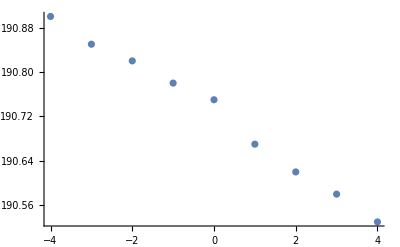

```mathematica
data={{0,190.75},{1,190.67},{2,190.62},{3,190.58},{4,190.53},{-1,190.78},{-2,190.82},{-3,190.85},{-4,190.90}};
errors={.0083,.0083,.0083,.0083,.0083,.0083,.0083,.0083,.0083};
Show[ListPlot[data],PlotRange->All]
```

In order to prepare the data for the linear fit, we need to get the data sets of d ∗ sin(θ) vs. m. The spacing d is already measured to be 0.00001016 m.

0.00001016

{{0,7.8768×10^-6},{1,8.36445×10^-6},{2,8.64224×10^-6},{3,8.84895×10^-6},{4,9.08739×10^-6},{-1,7.68077×10^-6},{-2,7.40867×10^-6},{-3,7.19679×10^-6},{-4,6.82937×10^-6}}

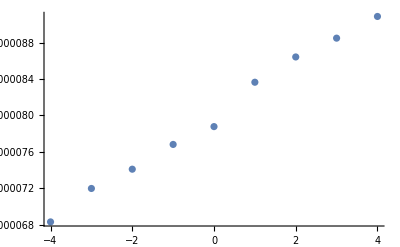

```mathematica
d= 0.00001016
data=data/.{x_,y_}->{x,d*Sin[y]}
Show[ListPlot[data],PlotRange->All]
```

## Linear Curve Fit

Or show an example of application ...

Next, I’ll apply the linear curve fit function y=ax+b to the prepared data, then the produced slope value is just the wavelength of the light source.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
lm=LinearModelFit[data,x,x,Weights->1/errors^2]
```

FittedModel[7.99283×10^-6+2.85656×10^-7 x]

```mathematica
lm["ANOVATableDegreesOfFreedom"]
```

{1,7,8}

190.722-0.0466667 x

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[{line},PlotStyle→Blue]].

## Another Linear Curve Fit

Add more sections as needed to explain the topic....

Another Curve Fit to eventually get the the velocity of sound in water (I’m working on this)

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)